```mathematica
SetDirectory["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data"];
```

## Quench GS,

```mathematica
SetDirectory["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_quench_GS"];
```

```mathematica
quenchKCW0 = Import["L12/complexity_Delta_1_L_12_w_0_R_10_pbc.txt","Table"]//Flatten;
quenchKCW0pt01 = Import["L12/complexity_Delta_1_L_12_w_0.01_R_10_pbc.txt","Table"]//Flatten;
quenchKCW0pt1 = Import["L12/complexity_Delta_1_L_12_w_0.1_R_10_pbc.txt","Table"]//Flatten;
quenchKCW0pt2 = Import["L12/complexity_Delta_1_L_12_w_0.2_R_10_pbc.txt","Table"]//Flatten;
quenchKCW0pt5 = Import["L12/complexity_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
quenchKCW1 = Import["L12/complexity_Delta_1_L_12_w_1_R_10_pbc.txt","Table"]//Flatten;
quenchKCW1pt5 = Import["L12/complexity_Delta_1_L_12_w_1.5_R_10_pbc.txt","Table"]//Flatten;
quenchKCW2 = Import["L12/complexity_Delta_1_L_12_w_2.0_R_10_pbc.txt","Table"]//Flatten;
quenchKCW2pt5 = Import["L12/complexity_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
quenchKCW3 = Import["L12/complexity_Delta_1_L_12_w_3.0_R_10_pbc.txt","Table"]//Flatten;
quenchKCW3pt5 = Import["L12/complexity_Delta_1_L_12_w_3.5_R_10_pbc.txt","Table"]//Flatten;
quenchKCW4 = Import["L12/complexity_Delta_1_L_12_w_4.0_R_10_pbc.txt","Table"]//Flatten;
quenchKCW4pt5 = Import["L12/complexity_Delta_1_L_12_w_4.5_R_10_pbc.txt","Table"]//Flatten;
quenchKCW5pt5 = Import["L12/complexity_Delta_1_L_12_w_5.5_R_10_pbc.txt","Table"]//Flatten;
tList = Import["L12/t_list_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW0 = Import["L12/krylov_IPR_Delta_1_L_12_w_0_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW0pt01 = Import["L12/krylov_IPR_Delta_1_L_12_w_0.01_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW0pt1 = Import["L12/krylov_IPR_Delta_1_L_12_w_0.1_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW0pt2 = Import["L12/krylov_IPR_Delta_1_L_12_w_0.2_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW0pt5 = Import["L12/krylov_IPR_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW1 = Import["L12/krylov_IPR_Delta_1_L_12_w_1_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW1pt5 = Import["L12/krylov_IPR_Delta_1_L_12_w_1.5_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW2 = Import["L12/krylov_IPR_Delta_1_L_12_w_2.0_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW2pt5 = Import["L12/krylov_IPR_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW3 = Import["L12/krylov_IPR_Delta_1_L_12_w_3.0_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW3pt5 = Import["L12/krylov_IPR_Delta_1_L_12_w_3.5_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW4 = Import["L12/krylov_IPR_Delta_1_L_12_w_4.0_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW4pt5 = Import["L12/krylov_IPR_Delta_1_L_12_w_4.5_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW5pt5 = Import["L12/krylov_IPR_Delta_1_L_12_w_5.5_R_10_pbc.txt","Table"]//Flatten;
quenchKEntW0 = Import["L12/krylov_entropy_Delta_1_L_12_w_0_R_10_pbc.txt","Table"]//Flatten;
quenchKECW0 = Exp[#]&/@quenchKEntW0;
quenchKEntW0pt01 = Import["L12/krylov_entropy_Delta_1_L_12_w_0.01_R_10_pbc.txt","Table"]//Flatten;
quenchKECW0pt01 = Exp[#]&/@quenchKEntW0pt01;
quenchKEntW0pt1 = Import["L12/krylov_entropy_Delta_1_L_12_w_0.1_R_10_pbc.txt","Table"]//Flatten;
quenchKECW0pt1 = Exp[#]&/@quenchKEntW0pt1;
quenchKEntW0pt2 = Import["L12/krylov_entropy_Delta_1_L_12_w_0.2_R_10_pbc.txt","Table"]//Flatten;
quenchKECW0pt2 = Exp[#]&/@quenchKEntW0pt2;
quenchKEntW0pt5 = Import["L12/krylov_entropy_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
quenchKECW0pt5 = Exp[#]&/@quenchKEntW0pt5;
quenchKEntW1 = Import["L12/krylov_entropy_Delta_1_L_12_w_1_R_10_pbc.txt","Table"]//Flatten;
quenchKECW1 = Exp[#]&/@quenchKEntW1;
quenchKEntW1pt5 = Import["L12/krylov_entropy_Delta_1_L_12_w_1.5_R_10_pbc.txt","Table"]//Flatten;
quenchKECW1pt5 = Exp[#]&/@quenchKEntW1pt5;
quenchKEntW2 = Import["L12/krylov_entropy_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
quenchKECW2 = Exp[#]&/@quenchKEntW2;
quenchKEntW2pt5 = Import["L12/krylov_entropy_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
quenchKECW2pt5 = Exp[#]&/@quenchKEntW2pt5;quenchKEntW3 = Import["L12/krylov_entropy_Delta_1_L_12_w_3.0_R_10_pbc.txt","Table"]//Flatten;
quenchKECW3 = Exp[#]&/@quenchKEntW3;
quenchKEntW3pt5 = Import["L12/krylov_entropy_Delta_1_L_12_w_3.5_R_10_pbc.txt","Table"]//Flatten;
quenchKECW3pt5 = Exp[#]&/@quenchKEntW3pt5;
quenchKEntW4 = Import["L12/krylov_entropy_Delta_1_L_12_w_4.0_R_10_pbc.txt","Table"]//Flatten;
quenchKECW4 = Exp[#]&/@quenchKEntW4;
quenchKEntW4pt5 = Import["L12/krylov_entropy_Delta_1_L_12_w_4.5_R_10_pbc.txt","Table"]//Flatten;
quechKECW4pt5 = Exp[#]&/@quenchKEntW4pt5;
quenchKEntW5pt5 = Import["L12/krylov_entropy_Delta_1_L_12_w_5.5_R_10_pbc.txt","Table"]//Flatten;
quenchKECW5pt5 = Exp[#]&/@quenchKEntW5pt5;
```

#### Normalized Complexity

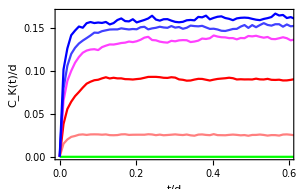
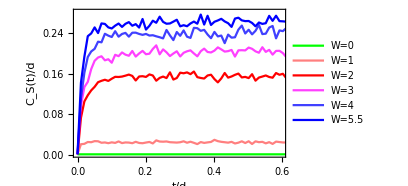
-Graphics- | -Graphics-

```mathematica
pKC1=Show[ListLinePlot[{Transpose[{tList,quenchKCW0}],Transpose[{tList,quenchKCW1}],Transpose[{tList,quenchKCW2}],Transpose[{tList,quenchKCW3}],Transpose[{tList,quenchKCW4}],Transpose[{tList,quenchKCW5pt5}]},PlotStyle->{RGBColor[0,1,0],RGBColor[1,0,0,0.5],RGBColor[1,0,0],RGBColor[1,0,1,0.75],RGBColor[0,0,1,0.75],RGBColor[0,0,1]}],Frame->True,LabelStyle->Directive[Bold, Black],PlotRange->{{0,0.6},All},FrameLabel->{Style["t/d",Bold,Black,12],Style["C_K(t)/d",Bold,Black,12]}];
pKIPR1=Show[ListLinePlot[{Transpose[{tList,924quenchKIPRW0}],Transpose[{tList,924quenchKIPRW1}],Transpose[{tList,924quenchKIPRW2}],Transpose[{tList,924quenchKIPRW3}],Transpose[{tList,924quenchKIPRW4}],Transpose[{tList,924quenchKIPRW5pt5}]},PlotStyle->{RGBColor[0,1,0],RGBColor[1,0,0,0.5],RGBColor[1,0,0],RGBColor[1,0,1,0.75],RGBColor[0,0,1,0.75],RGBColor[0,0,1]}],Frame->True,LabelStyle->Directive[Bold, Black],PlotRange->{{0,0.6},Full},FrameLabel->{Style["t/d",Bold,Black,12],Style["d x I_K(t)",Bold,Black,12]}];
pKEC1=Show[ListLinePlot[{Transpose[{tList,quenchKECW0/924}],Transpose[{tList,quenchKECW1/924}],Transpose[{tList,quenchKECW2/924}],Transpose[{tList,quenchKECW3/924}],Transpose[{tList,quenchKECW4/924}],Transpose[{tList,quenchKECW5pt5/924}]},PlotStyle->{RGBColor[0,1,0],RGBColor[1,0,0,0.5],RGBColor[1,0,0],RGBColor[1,0,1,0.75],RGBColor[0,0,1,0.75],RGBColor[0,0,1]},PlotLegends->{Style["W=0",10],Style["W=1",10],Style["W=2",10],Style["W=3",10],Style["W=4",10],Style["W=5.5",10]}],Frame->True,LabelStyle->Directive[Bold, Black],PlotRange->{{0,0.6},All},FrameLabel->{Style["t/d",Bold,Black,12],Style["C_S(t)/d",Bold,Black,12]}];


Grid[{{pKC1,pKEC1}}]
```

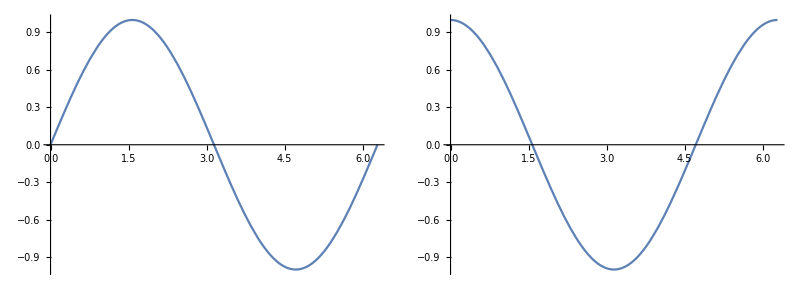

```mathematica
plot1=Plot[Sin[x],{x,0,2 Pi}];
plot2=Plot[Cos[x],{x,0,2 Pi}];

Grid[{{plot1,plot2}}]
```

```mathematica
quenchKECW0pt1
```

```mathematica
Export["/Users/aneekphys/Documents/MBL1 plots/QuechGS_KC_KECL12.pdf",%2831]
```

/Users/aneekphys/Documents/MBL1 plots/QuechGS_KC_KECL12.pdf

## Quench GS,

```mathematica
SetDirectory["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_quench_MBL_GS"];
```

```mathematica
quenchKCW0 = Import["L12/complexity_Delta_1_L_12_w_0_R_10_pbc.txt","Table"]//Flatten;
quenchKCW0pt01 = Import["L12/complexity_Delta_1_L_12_w_0.01_R_10_pbc.txt","Table"]//Flatten;
quenchKCW0pt1 = Import["L12/complexity_Delta_1_L_12_w_0.1_R_10_pbc.txt","Table"]//Flatten;
quenchKCW0pt2 = Import["L12/complexity_Delta_1_L_12_w_0.2_R_10_pbc.txt","Table"]//Flatten;
quenchKCW0pt5 = Import["L12/complexity_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
quenchKCW1 = Import["L12/complexity_Delta_1_L_12_w_1_R_10_pbc.txt","Table"]//Flatten;
quenchKCW1pt5 = Import["L12/complexity_Delta_1_L_12_w_1.5_R_10_pbc.txt","Table"]//Flatten;
quenchKCW2 = Import["L12/complexity_Delta_1_L_12_w_2.0_R_10_pbc.txt","Table"]//Flatten;
quenchKCW2pt5 = Import["L12/complexity_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
quenchKCW3 = Import["L12/complexity_Delta_1_L_12_w_3.0_R_10_pbc.txt","Table"]//Flatten;
quenchKCW3pt5 = Import["L12/complexity_Delta_1_L_12_w_3.5_R_10_pbc.txt","Table"]//Flatten;
quenchKCW4 = Import["L12/complexity_Delta_1_L_12_w_4.0_R_10_pbc.txt","Table"]//Flatten;
quenchKCW4pt5 = Import["L12/complexity_Delta_1_L_12_w_4.5_R_10_pbc.txt","Table"]//Flatten;
quenchKCW5pt5 = Import["L12/complexity_Delta_1_L_12_w_5.5_R_10_pbc.txt","Table"]//Flatten;
tList = Import["L12/t_list_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW0 = Import["L12/krylov_IPR_Delta_1_L_12_w_0_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW0pt01 = Import["L12/krylov_IPR_Delta_1_L_12_w_0.01_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW0pt1 = Import["L12/krylov_IPR_Delta_1_L_12_w_0.1_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW0pt2 = Import["L12/krylov_IPR_Delta_1_L_12_w_0.2_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW0pt5 = Import["L12/krylov_IPR_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW1 = Import["L12/krylov_IPR_Delta_1_L_12_w_1_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW1pt5 = Import["L12/krylov_IPR_Delta_1_L_12_w_1.5_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW2 = Import["L12/krylov_IPR_Delta_1_L_12_w_2.0_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW2pt5 = Import["L12/krylov_IPR_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW3 = Import["L12/krylov_IPR_Delta_1_L_12_w_3.0_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW3pt5 = Import["L12/krylov_IPR_Delta_1_L_12_w_3.5_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW4 = Import["L12/krylov_IPR_Delta_1_L_12_w_4.0_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW4pt5 = Import["L12/krylov_IPR_Delta_1_L_12_w_4.5_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW5pt5 = Import["L12/krylov_IPR_Delta_1_L_12_w_5.5_R_10_pbc.txt","Table"]//Flatten;
quenchKEntW0 = Import["L12/krylov_entropy_Delta_1_L_12_w_0_R_10_pbc.txt","Table"]//Flatten;
quenchKECW0 = Exp[#]&/@quenchKEntW0;
quenchKEntW0pt01 = Import["L12/krylov_entropy_Delta_1_L_12_w_0.01_R_10_pbc.txt","Table"]//Flatten;
quenchKECW0pt01 = Exp[#]&/@quenchKEntW0pt01;
quenchKEntW0pt1 = Import["L12/krylov_entropy_Delta_1_L_12_w_0.1_R_10_pbc.txt","Table"]//Flatten;
quenchKECW0pt1 = Exp[#]&/@quenchKEntW0pt1;
quenchKEntW0pt2 = Import["L12/krylov_entropy_Delta_1_L_12_w_0.2_R_10_pbc.txt","Table"]//Flatten;
quenchKECW0pt2 = Exp[#]&/@quenchKEntW0pt2;
quenchKEntW0pt5 = Import["L12/krylov_entropy_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
quenchKECW0pt5 = Exp[#]&/@quenchKEntW0pt5;
quenchKEntW1 = Import["L12/krylov_entropy_Delta_1_L_12_w_1_R_10_pbc.txt","Table"]//Flatten;
quenchKECW1 = Exp[#]&/@quenchKEntW1;
quenchKEntW1pt5 = Import["L12/krylov_entropy_Delta_1_L_12_w_1.5_R_10_pbc.txt","Table"]//Flatten;
quenchKECW1pt5 = Exp[#]&/@quenchKEntW1pt5;
quenchKEntW2 = Import["L12/krylov_entropy_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
quenchKECW2 = Exp[#]&/@quenchKEntW2;
quenchKEntW2pt5 = Import["L12/krylov_entropy_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
quenchKECW2pt5 = Exp[#]&/@quenchKEntW2pt5;quenchKEntW3 = Import["L12/krylov_entropy_Delta_1_L_12_w_3.0_R_10_pbc.txt","Table"]//Flatten;
quenchKECW3 = Exp[#]&/@quenchKEntW3;
quenchKEntW3pt5 = Import["L12/krylov_entropy_Delta_1_L_12_w_3.5_R_10_pbc.txt","Table"]//Flatten;
quenchKECW3pt5 = Exp[#]&/@quenchKEntW3pt5;
quenchKEntW4 = Import["L12/krylov_entropy_Delta_1_L_12_w_4.0_R_10_pbc.txt","Table"]//Flatten;
quenchKECW4 = Exp[#]&/@quenchKEntW4;
quenchKEntW4pt5 = Import["L12/krylov_entropy_Delta_1_L_12_w_4.5_R_10_pbc.txt","Table"]//Flatten;
quechKECW4pt5 = Exp[#]&/@quenchKEntW4pt5;
quenchKEntW5pt5 = Import["L12/krylov_entropy_Delta_1_L_12_w_5.5_R_10_pbc.txt","Table"]//Flatten;
quenchKECW5pt5 = Exp[#]&/@quenchKEntW5pt5;
```

#### Normalized Complexity

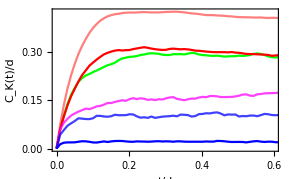
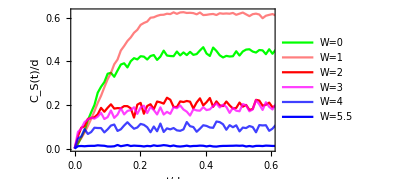
-Graphics- | -Graphics-

```mathematica
pKC1=Show[ListLinePlot[{Transpose[{tList,quenchKCW0}],Transpose[{tList,quenchKCW1}],Transpose[{tList,quenchKCW2}],Transpose[{tList,quenchKCW3}],Transpose[{tList,quenchKCW4}],Transpose[{tList,quenchKCW5pt5}]},PlotStyle->{RGBColor[0,1,0],RGBColor[1,0,0,0.5],RGBColor[1,0,0],RGBColor[1,0,1,0.75],RGBColor[0,0,1,0.75],RGBColor[0,0,1]}],Frame->True,LabelStyle->Directive[Bold, Black],PlotRange->{{0,0.6},All},FrameLabel->{Style["t/d",Bold,Black,12],Style["C_K(t)/d",Bold,Black,12]}];
pKIPR1=Show[ListLinePlot[{Transpose[{tList,924quenchKIPRW0}],Transpose[{tList,924quenchKIPRW1}],Transpose[{tList,924quenchKIPRW2}],Transpose[{tList,924quenchKIPRW3}],Transpose[{tList,924quenchKIPRW4}],Transpose[{tList,924quenchKIPRW5pt5}]},PlotStyle->{RGBColor[0,1,0],RGBColor[1,0,0,0.5],RGBColor[1,0,0],RGBColor[1,0,1,0.75],RGBColor[0,0,1,0.75],RGBColor[0,0,1]}],Frame->True,LabelStyle->Directive[Bold, Black],PlotRange->{{0,0.6},Full},FrameLabel->{Style["t/d",Bold,Black,12],Style["d x I_K(t)",Bold,Black,12]}];
pKEC1=Show[ListLinePlot[{Transpose[{tList,quenchKECW0/924}],Transpose[{tList,quenchKECW1/924}],Transpose[{tList,quenchKECW2/924}],Transpose[{tList,quenchKECW3/924}],Transpose[{tList,quenchKECW4/924}],Transpose[{tList,quenchKECW5pt5/924}]},PlotStyle->{RGBColor[0,1,0],RGBColor[1,0,0,0.5],RGBColor[1,0,0],RGBColor[1,0,1,0.75],RGBColor[0,0,1,0.75],RGBColor[0,0,1]},PlotLegends->{Style["W=0",10],Style["W=1",10],Style["W=2",10],Style["W=3",10],Style["W=4",10],Style["W=5.5",10]}],Frame->True,LabelStyle->Directive[Bold, Black],PlotRange->{{0,0.6},All},FrameLabel->{Style["t/d",Bold,Black,12],Style["C_S(t)/d",Bold,Black,12]}];


Grid[{{pKC1,pKEC1}}]
```

```mathematica
plot1=Plot[Sin[x],{x,0,2 Pi}];
plot2=Plot[Cos[x],{x,0,2 Pi}];

Grid[{{plot1,plot2}}]
```

-Graphics-

```mathematica
quenchKECW0pt1
```

```mathematica
Export["/Users/aneekphys/Documents/MBL1 plots/QuechGS_KC_KECL12.pdf",%2831]
```

/Users/aneekphys/Documents/MBL1 plots/QuechGS_KC_KECL12.pdf

## Quench TFD,

```mathematica
SetDirectory["/Users/aneekphys/Library/CloudStorage/OneDrive-IndianInstituteofScience/Projects/MBL_SYK_project/MBL_Data/Delta1_lamb0_quench_TFD"];
```

```mathematica
quenchKCW0 = Import["L12/complexity_Delta_1_L_12_w_0_R_10_pbc.txt","Table"]//Flatten;
quenchKCW0pt01 = Import["L12/complexity_Delta_1_L_12_w_0.01_R_10_pbc.txt","Table"]//Flatten;
quenchKCW0pt1 = Import["L12/complexity_Delta_1_L_12_w_0.1_R_10_pbc.txt","Table"]//Flatten;
quenchKCW0pt2 = Import["L12/complexity_Delta_1_L_12_w_0.2_R_10_pbc.txt","Table"]//Flatten;
quenchKCW0pt5 = Import["L12/complexity_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
quenchKCW1 = Import["L12/complexity_Delta_1_L_12_w_1_R_10_pbc.txt","Table"]//Flatten;
quenchKCW1pt5 = Import["L12/complexity_Delta_1_L_12_w_1.5_R_10_pbc.txt","Table"]//Flatten;
quenchKCW2 = Import["L12/complexity_Delta_1_L_12_w_2.0_R_10_pbc.txt","Table"]//Flatten;
quenchKCW2pt5 = Import["L12/complexity_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
quenchKCW3 = Import["L12/complexity_Delta_1_L_12_w_3.0_R_10_pbc.txt","Table"]//Flatten;
quenchKCW3pt5 = Import["L12/complexity_Delta_1_L_12_w_3.5_R_10_pbc.txt","Table"]//Flatten;
quenchKCW4 = Import["L12/complexity_Delta_1_L_12_w_4.0_R_10_pbc.txt","Table"]//Flatten;
quenchKCW4pt5 = Import["L12/complexity_Delta_1_L_12_w_4.5_R_10_pbc.txt","Table"]//Flatten;
quenchKCW5pt5 = Import["L12/complexity_Delta_1_L_12_w_5.5_R_10_pbc.txt","Table"]//Flatten;
tList = Import["L12/t_list_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW0 = Import["L12/krylov_IPR_Delta_1_L_12_w_0_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW0pt01 = Import["L12/krylov_IPR_Delta_1_L_12_w_0.01_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW0pt1 = Import["L12/krylov_IPR_Delta_1_L_12_w_0.1_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW0pt2 = Import["L12/krylov_IPR_Delta_1_L_12_w_0.2_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW0pt5 = Import["L12/krylov_IPR_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW1 = Import["L12/krylov_IPR_Delta_1_L_12_w_1_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW1pt5 = Import["L12/krylov_IPR_Delta_1_L_12_w_1.5_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW2 = Import["L12/krylov_IPR_Delta_1_L_12_w_2.0_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW2pt5 = Import["L12/krylov_IPR_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW3 = Import["L12/krylov_IPR_Delta_1_L_12_w_3.0_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW3pt5 = Import["L12/krylov_IPR_Delta_1_L_12_w_3.5_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW4 = Import["L12/krylov_IPR_Delta_1_L_12_w_4.0_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW4pt5 = Import["L12/krylov_IPR_Delta_1_L_12_w_4.5_R_10_pbc.txt","Table"]//Flatten;
quenchKIPRW5pt5 = Import["L12/krylov_IPR_Delta_1_L_12_w_5.5_R_10_pbc.txt","Table"]//Flatten;
quenchKEntW0 = Import["L12/krylov_entropy_Delta_1_L_12_w_0_R_10_pbc.txt","Table"]//Flatten;
quenchKECW0 = Exp[#]&/@quenchKEntW0;
quenchKEntW0pt01 = Import["L12/krylov_entropy_Delta_1_L_12_w_0.01_R_10_pbc.txt","Table"]//Flatten;
quenchKECW0pt01 = Exp[#]&/@quenchKEntW0pt01;
quenchKEntW0pt1 = Import["L12/krylov_entropy_Delta_1_L_12_w_0.1_R_10_pbc.txt","Table"]//Flatten;
quenchKECW0pt1 = Exp[#]&/@quenchKEntW0pt1;
quenchKEntW0pt2 = Import["L12/krylov_entropy_Delta_1_L_12_w_0.2_R_10_pbc.txt","Table"]//Flatten;
quenchKECW0pt2 = Exp[#]&/@quenchKEntW0pt2;
quenchKEntW0pt5 = Import["L12/krylov_entropy_Delta_1_L_12_w_0.5_R_10_pbc.txt","Table"]//Flatten;
quenchKECW0pt5 = Exp[#]&/@quenchKEntW0pt5;
quenchKEntW1 = Import["L12/krylov_entropy_Delta_1_L_12_w_1_R_10_pbc.txt","Table"]//Flatten;
quenchKECW1 = Exp[#]&/@quenchKEntW1;
quenchKEntW1pt5 = Import["L12/krylov_entropy_Delta_1_L_12_w_1.5_R_10_pbc.txt","Table"]//Flatten;
quenchKECW1pt5 = Exp[#]&/@quenchKEntW1pt5;
quenchKEntW2 = Import["L12/krylov_entropy_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
quenchKECW2 = Exp[#]&/@quenchKEntW2;
quenchKEntW2pt5 = Import["L12/krylov_entropy_Delta_1_L_12_w_2.5_R_10_pbc.txt","Table"]//Flatten;
quenchKECW2pt5 = Exp[#]&/@quenchKEntW2pt5;quenchKEntW3 = Import["L12/krylov_entropy_Delta_1_L_12_w_3.0_R_10_pbc.txt","Table"]//Flatten;
quenchKECW3 = Exp[#]&/@quenchKEntW3;
quenchKEntW3pt5 = Import["L12/krylov_entropy_Delta_1_L_12_w_3.5_R_10_pbc.txt","Table"]//Flatten;
quenchKECW3pt5 = Exp[#]&/@quenchKEntW3pt5;
quenchKEntW4 = Import["L12/krylov_entropy_Delta_1_L_12_w_4.0_R_10_pbc.txt","Table"]//Flatten;
quenchKECW4 = Exp[#]&/@quenchKEntW4;
quenchKEntW4pt5 = Import["L12/krylov_entropy_Delta_1_L_12_w_4.5_R_10_pbc.txt","Table"]//Flatten;
quechKECW4pt5 = Exp[#]&/@quenchKEntW4pt5;
quenchKEntW5pt5 = Import["L12/krylov_entropy_Delta_1_L_12_w_5.5_R_10_pbc.txt","Table"]//Flatten;
quenchKECW5pt5 = Exp[#]&/@quenchKEntW5pt5;
```

#### Normalized Complexity

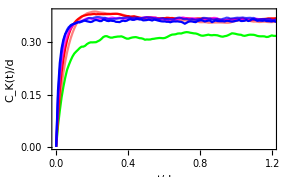
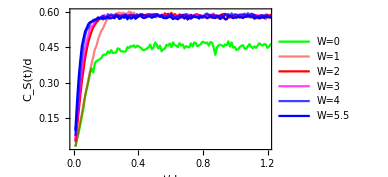
-Graphics- | -Graphics-

```mathematica
pKC1=Show[ListLinePlot[{Transpose[{tList,quenchKCW0}],Transpose[{tList,quenchKCW1}],Transpose[{tList,quenchKCW2}],Transpose[{tList,quenchKCW3}],Transpose[{tList,quenchKCW4}],Transpose[{tList,quenchKCW5pt5}]},PlotStyle->{RGBColor[0,1,0],RGBColor[1,0,0,0.5],RGBColor[1,0,0],RGBColor[1,0,1,0.75],RGBColor[0,0,1,0.75],RGBColor[0,0,1]},PlotRange->{{0,1.2},All}],Frame->True,LabelStyle->Directive[Bold, Black],FrameLabel->{Style["t/d",Bold,Black,12],Style["C_K(t)/d",Bold,Black,12]}];
pKIPR1=Show[ListLinePlot[{Transpose[{tList,924quenchKIPRW0}],Transpose[{tList,924quenchKIPRW1}],Transpose[{tList,924quenchKIPRW2}],Transpose[{tList,924quenchKIPRW3}],Transpose[{tList,924quenchKIPRW4}],Transpose[{tList,924quenchKIPRW5pt5}]},PlotStyle->{RGBColor[0,1,0],RGBColor[1,0,0,0.5],RGBColor[1,0,0],RGBColor[1,0,1,0.75],RGBColor[0,0,1,0.75],RGBColor[0,0,1]}],Frame->True,LabelStyle->Directive[Bold, Black],PlotRange->{{0,0.6},Full},FrameLabel->{Style["t/d",Bold,Black,12],Style["d x I_K(t)",Bold,Black,12]}];
pKEC1=Show[ListLinePlot[{Transpose[{tList,quenchKECW0/924}],Transpose[{tList,quenchKECW1/924}],Transpose[{tList,quenchKECW2/924}],Transpose[{tList,quenchKECW3/924}],Transpose[{tList,quenchKECW4/924}],Transpose[{tList,quenchKECW5pt5/924}]},PlotStyle->{RGBColor[0,1,0],RGBColor[1,0,0,0.5],RGBColor[1,0,0],RGBColor[1,0,1,0.75],RGBColor[0,0,1,0.75],RGBColor[0,0,1]},PlotLegends->{Style["W=0",10],Style["W=1",10],Style["W=2",10],Style["W=3",10],Style["W=4",10],Style["W=5.5",10]}],Frame->True,LabelStyle->Directive[Bold, Black],PlotRange->{{0,1.2},All},FrameLabel->{Style["t/d",Bold,Black,12],Style["C_S(t)/d",Bold,Black,12]}];


Grid[{{pKC1,pKEC1}}]
```

```mathematica
plot1=Plot[Sin[x],{x,0,2 Pi}];
plot2=Plot[Cos[x],{x,0,2 Pi}];

Grid[{{plot1,plot2}}]
```

-Graphics-

```mathematica
quenchKECW0pt1
```

```mathematica
Export["/Users/aneekphys/Documents/MBL1 plots/QuechGS_KC_KECL12.pdf",%2831]
```

/Users/aneekphys/Documents/MBL1 plots/QuechGS_KC_KECL12.pdf